```mathematica
SetDirectory["/home/jamie/simionwork/efields/"];
filenames = 
Last/@Sort[{Characters@#,#}&/@FileNames["cylinder_E"~~__~~"L27_"~~"X"|"Y"|"Z"~~".dat"]];
data = 0.1*Drop[Import/@filenames,0,8];
dataxyzs=Transpose[Partition[data,3]];
```

```mathematica
switchElectrodes[{start_,end_},volts_]:=Module[{dat=dataxyzs},For[i=1,i≤3,i++,dat[[i]][[start;;end]]*=volts];Return[dat]];
magnitude[dat_List]:=√(((Total/@dat)[[1]])^2+((Total/@dat)[[2]])^2+((Total/@dat)[[3]])^2);
```

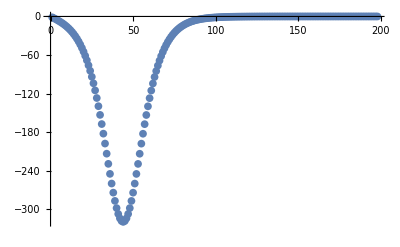

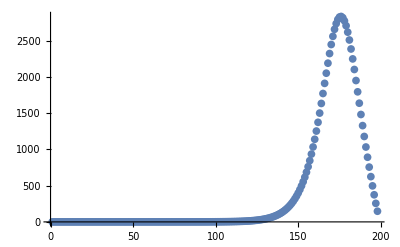

z→162.346

InterpolatingFunction::dmval: Input value {0.00408571} lies outside the range of data in the interpolating function. Extrapolation will be used.

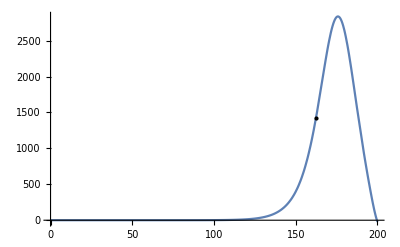

```mathematica
ListPlot[Sum[dataxyzs[[3]][[i]][[All,26]],{i,1,28}],PlotRange->All]
ListPlot[magnitude[switchElectrodes[{1,4},10]][[All,26]]]
mf = ListInterpolation[magnitude[switchElectrodes[{1,4},10]][[All,26]]];
FindRoot[Max[magnitude[switchElectrodes[{1,4},10]][[All,26]]]/2 == mf[z],{z,160}][[1]]
Show[{Plot[mf[z],{z,0,200}],Graphics[Point[{z/.%,Max[magnitude[switchElectrodes[{1,4},10]][[All,26]]]/2}]]}]
```

```mathematica
Clear["V"]
FX[bigN_Integer,r_,d_]:=150(Sum[V[n]/(((z-n d)^2+r^2)^(3/2))-V[n]/(r((z-d(n-1))^2+r^2)^(3/2))-V[n]/(r((z-d(n+1))^2+r^2)^(3/2)),{n,0,bigN}]-(V[0]/(r(z^2+r^2)^(3/2))-V[0]/(r((z+d)^2+r^2)^(3/2))))/.z->0.15z
FZ[bigN_Integer,r_,d_]:=2500(Sum[(+V[n])/(((z-d(n-1/2))^2+r^2)^(3/2))+(-V[n])/(((z-d(n+1/2))^2+r^2)^(3/2)),{n,0,bigN}]-V[0]/(((z+d/2)^2+r^2)^(3/2)))/.z->0.14(z+6)
FF[bigN_Integer,r_,d_]:=√(2 FX[bigN,r,d]^2+FZ[bigN,r,d]^2)
```

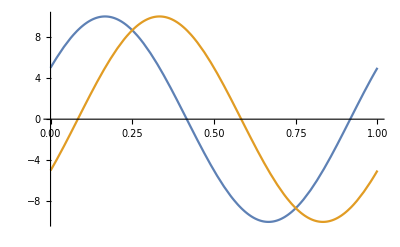

```mathematica
myExp[t_,c_:1]:=(Exp[c t] - 1)/(Exp[c] - 1);
Clear["V"];
V[n_,t_]:=10Cos[-2π t +(n π)/3]
(*V[n_,t_]:=1*)
(*Plot[Evaluate[FF[6,2,3]/.V[n_]->V[n,t]],{z,0,110}]*)
Plot[Evaluate@Table[V[n,t],{n,1,2}],{t,0,1}]
```

```mathematica
Clear["V"]
V[n_/;n≤6,t_]:=120Cos[(8 π n / 36)-1/2 π 0.1 t^2]
V[n_/;n>6,t_]:=0
V[0]=V[1];
Animate[{Plot[Evaluate[FF[9,20,22]/.V[n_]->V[n,t]],{z,0,2000},ImageSize->Large,PlotRange->{All,{0,200}}]},{t,0,10}]
```

```mathematica
myP[n_,t_]:=Cos[8π n/36 - (t*0.000001)^2 π 500 / (20 10^-3×0.9 0.0004)];
```

```mathematica
Animate[BarChart[Table[myP[n,t],{n,1,9}]],{t,0,0.0004/0.000001}]
```

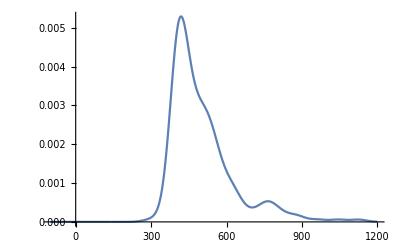

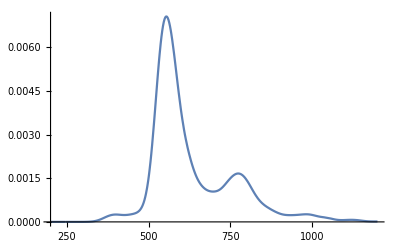

```mathematica
veld= SmoothKernelDistribution[Import["/home/jamie/simionwork/vOut.dat"][[1]]]//PDF;
Plot[veld[z],{z,-100,1200},PlotRange->All]
```

```mathematica
myAZ[E_,z_]:=1000(E[[z+1]]-E[[z-1]])/2.*3/2*(-1.60217657*^-19)*(5.2917721092*^-11)*25*12/(1.6737*^27);
```

```mathematica
rawPos = Import["/home/jamie/simionwork/pOut.dat"];
rawE = Import["/home/jamie/simionwork/eOut.dat"];
meshPos = Transpose[PadRight[rawPos,{Length@rawPos,Max[Length/@rawPos]},pad]]/.pad->Sequence[];
Manipulate[Show[{ListLinePlot[rawE[[t]],PlotRange->{0,190000},Mesh->{meshPos[[t]]},MeshStyle->{PointSize[Medium]},MeshFunctions->{#1&,#2&}]
}],
{t,1,Length[rawE],1}]
```

Part::partw: Part 600 of {{28.6, 11.8241, 22.4629, 29.4536, 61.981, 3.48721, 29.7984, 17.9491, 5.8692, 41.2847, 65.7267, 27.9877, 49.3644, 26.3216, 36.0034, 58.4555, 41.6253, 39.0891, 26.1706, 20.6329, 3.82607, 21.0985, 54.7867, 32.6411, 38.8029, 29.0096, 5.45899, 61.1168, 11.5188, 2.43108, 60.9428, 47.7543, 46.0618, 44.7913, 11.2075, 64.6542, 13.2306, 1.44914, 53.1318, 19.3838, 23.406, 34.6859, 7.65024, 51.1518, 37.6577, 39.0415, 36.9567, 27.7566, 12.1994, 3.59862, « 950 »}, « 49 », « 537 »} does not exist.

Mesh::ilevels: {{28.6, 11.8241, 22.4629, 29.4536, 61.981, 3.48721, 29.7984, 17.9491, 5.8692, 41.2847, 65.7267, 27.9877, 49.3644, 26.3216, 36.0034, 58.4555, 41.6253, 39.0891, 26.1706, 20.6329, 3.82607, 21.0985, 54.7867, 32.6411, 38.8029, 29.0096, 5.45899, 61.1168, 11.5188, 2.43108, 60.9428, 47.7543, 46.0618, 44.7913, 11.2075, 64.6542, 13.2306, 1.44914, 53.1318, 19.3838, 23.406, 34.6859, 7.65024, 51.1518, 37.6577, 39.0415, 36.9567, 27.7566, 12.1994, 3.59862, « 950 »}, « 49 », « 537 »} ⟦ 600 ⟧ is not a valid mesh specification.

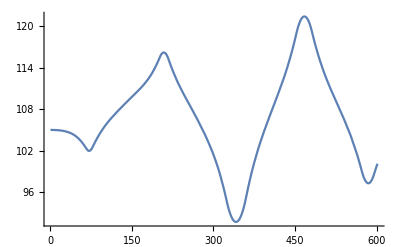

```mathematica
posf1 = Interpolation[rawPos[[1]]]
posf2 = Interpolation[rawPos[[2]]]
Plot[posf1[x]+posf2[x],{x,1,601}]
```

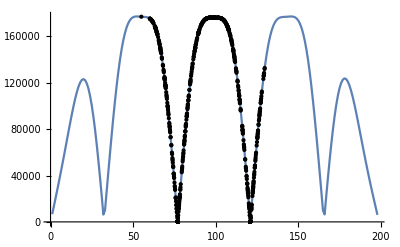

```mathematica
eiOut = Import["/home/jamie/simionwork/eiOut.dat"][[1]];
eiOut = Transpose[{Range[Length@eiOut],eiOut}];
ListLinePlot[eiOut,Mesh->{(Transpose[PadRight[rawPos,{Max[Length/@rawPos],Length@rawPos},pad]]/.pad->Sequence[])[[1]]},MeshStyle->PointSize[Medium],MeshFunctions->{#1&,#2&}]
```

```mathematica
Table[Cos[8π n/36],{n,1,9}]//N
```

{0.766044,0.173648,-0.5,-0.939693,-0.939693,-0.5,0.173648,0.766044,1.}

```mathematica
2.4*10^4*1.2*10^-2
```

288.

```mathematica
Table[Mod[(i/4 + 1),4],{i,0,35,4}]
```

{1,2,3,0,1,2,3,0,1}

```mathematica
Mod[3,4]
```

3

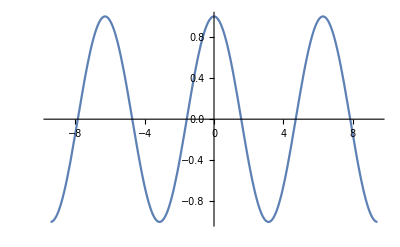

```mathematica
Plot[Cos[x],{x,-3π,3π}]
```